```mathematica
data=Import["/Users/wanglong/task/fort.102","Table"];
```

```mathematica
sp=9;
offset=Table[IntegerPart[Length@data/sp]+IntegerPart[ArcTan[Mod[Length@data,sp]/j]/π*4],{j,sp}];
data1=Table[data[[i+Plus@@offset[[1;;j-1]]]],{j,sp},{i,offset[[j]]}];
data1s=Table[{i,Plus@@data1[[i,All,2]]},{i,Length@data1}];
data2=Table[data[[sp*(i-1)+j]],{j,sp},{i,offset[[j]]}];
data2s=Table[{i,Plus@@data2[[i,All,2]]},{i,Length@data2}];
```

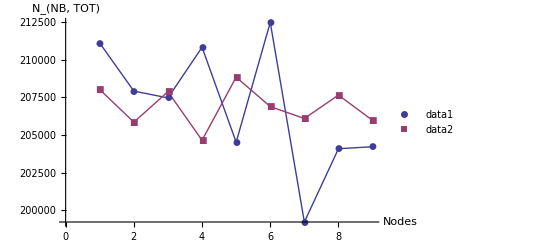
data1 | 649 | 649 | 648 | 648 | 648 | 648 | 648 | 648 | 648
data2 | 649 | 649 | 648 | 648 | 648 | 648 | 648 | 648 | 648
-Graphics-

```mathematica
Column[{
Grid[MapThread[Prepend,{(Length/@#)&/@{data1,data2},{"data1","data2"}}],Frame->All],
ListPlot[{data1s,data2s},PlotMarkers->{Automatic},AxesLabel->{"Nodes","N_(NB, TOT)"},ImageSize->400,Joined->True,PlotLegends->{"data1","data2"}]}]
```